```mathematica
<<Units`
```

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### Mass m, kinetic energy ϵ incident on a target M

```mathematica
Solve[ReplaceAll[(γ-1)m==ϵ,γ->1/Sqrt[1-β^2]],β]
```

{{β→-(√ϵ √(2 m+ϵ))/(m+ϵ)},{β→(√ϵ √(2 m+ϵ))/(m+ϵ)}}

#### Rutherford cross section for energy loss Ed (classical, spin-0 and spin-1/2)

```mathematica
rutherford=(2Pi α^2 Z^2)/(M β^2 Ed^2);
```

```mathematica
rutherford0=(2Pi α^2 Z^2)/(M β^2 Ed^2)(1-β^2 Ed/ekin);
```

```mathematica
rutherford2=(2Pi α^2 Z^2)/(M β^2 Ed^2)(1-β^2 Ed/ekin+1/2(Ed/(ϵ+m))^2);
```

#### For simple rutherford xc, dE/dx is purely logarithmic

```mathematica
Integrate[rutherford*n*Ed,{Ed,emin,emax},Assumptions->{Ed>0,emin>0,emax>emin}]
```

(2 n π Z^2 α^2 Log[emax/emin])/(M β^2)

```mathematica
SP=(2n π Z^2 α^2 Log[(emax/emin)])/(M β^2);
```

```mathematica
Integrate[rutherford0*n*Ed,{Ed,emin,emax},Assumptions->{Ed>0,emin>0,emax>emin}]/.ekin->Ekin
```

(n π Z^2 α^2 (1+M^2/m^2+(2 M γ)/m) ((-emax+emin) β^2+(2 M β^2 γ^2 Log[emax/emin])/(1+M^2/m^2+(2 M γ)/m)))/(M^2 β^4 γ^2)

```mathematica
Integrate[rutherford2*npaulirel*Ed,{Ed,emin,emax},Assumptions->{Ed>0,emin>0,emax>emin}]
```

1/(180 M π β^2)Z^2 α^2 (360 Ef^2 (emax-emin)+180 Ef (-emax^2+emin^2)+40 (emax^3-emin^3)+(180 Ef^2 (-emax^2+emin^2) β^2)/ekin+(120 Ef (emax^3-emin^3) β^2)/ekin+(30 (-emax^4+emin^4) β^2)/ekin+(60 Ef^2 (emax^3-emin^3))/(m+ϵ)^2+(45 Ef (-emax^4+emin^4))/(m+ϵ)^2+(12 (emax^5-emin^5))/(m+ϵ)^2)

#### Scattering off Degenerate Targets, Fermi Energy Ef

```mathematica
npaulirel:=Integrate[e^2/Pi^2,{e,Ef-Ed,Ef}]
```

```mathematica
Convert[10^33 Centimeter^-3*(200 Mega ElectronVolt*Fermi)^3,(Mega ElectronVolt)^3]
```

8 ElectronVolt^3 Mega^3

```mathematica
ReplaceAll[npaulirel,Ed->Ef]
```

Ef^3/(3 π^2)

```mathematica
(3 Pi^2 n)^(1/3)/.n->8
```

2 3^(1/3) π^(2/3)

```mathematica
plotrel=Plot[ReplaceAll[npaulirel,{Ef->2 3^(1/3) π^(2/3),n->8}],{Ed,0,2 3^(1/3) π^(2/3)}];naiveplot=Plot[ReplaceAll[n*(Ed/Ef),{Ef->2 3^(1/3) π^(2/3),n->8}],{Ed,0,2 3^(1/3) π^(2/3)}];
```

#### Compare effective number density with naive Pauli-blocking factor - upper end of plot is Ef

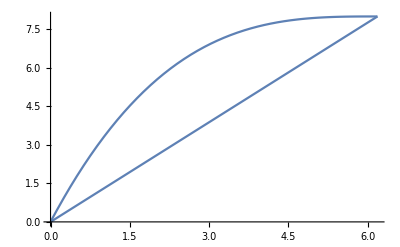

```mathematica
Show[plotrel,naiveplot]
```

#### Coulomb Log Emax

```mathematica
collision[b_]:=(2 Z^2 α^2)/(M b^2 β^2)
```

```mathematica
Ekin=(2M β^2 γ^2)/(1+2γ (M/m)+(M/m)^2);
```

```mathematica
Equant=collision[1/(Min[m,M]β*γ)]
```

(2 Z^2 α^2 γ^2 Min[m,M]^2)/M

#### Coulomb Log Emin

```mathematica
λTF=((6Pi Z α n)/Ef)^(-1/2);
```

```mathematica
Esc=collision[λTF]
```

(12 n π Z^3 α^3)/(Ef M β^2)

```mathematica
Elattice:=(Z^2 α)/(n/Z)^(-1/3)
```

```mathematica
Elattice/((α*Z)/(λTF*β)(α Z^2/M*(n/Z)^(1/3))^(1/2))//FullSimplify
```

```mathematica
(M n √(((n/Z)^(1/3) Z^2 α)/M) β)/(Ef √(6 π) ((n Z α)/Ef)^(3/2))*(n/Z*Z*α^2*1/(M*β^2))//FullSimplify
```

```mathematica
(Ef √((n Z α)/Ef) √(((n/Z)^(1/3) Z^2 α)/M))/(√(6 π) Z^2 β)/.{Ef->(3 Pi^2 n)^(1/3),β->1}//N
```

```mathematica
(0.4051224139776965 n^(1/3) √(n^(2/3) Z α) √(((n/Z)^(1/3) Z^2 α)/M))/Z^2/.{M->10000,α->1/137,Z->6,n->8}
```

0.0000506609

#### SP in units of MeV/(10^-5 cm)

```mathematica
Convert[(Mega ElectronVolt)^2 1/(200 Mega ElectronVolt*Fermi),(Mega ElectronVolt)/Centimeter]//N
```

(5.×10^10 ElectronVolt Mega)/Centimeter

#### Stopping power due to Coulomb Collisions off carbon nuclei

```mathematica
dedx:=ReplaceAll[ReplaceAll[ReplaceAll[ReplaceAll[1/Z SP,{emin->Max[Esc,Elattice],emax->Min[Ekin,Equant,M]}],Ef->(3 Pi^2 n)^(1/3)],γ->1/Sqrt[1-β^2]],β->(√ϵ √(2 m+ϵ))/(m+ϵ)];
```

```mathematica
electron=LogLogPlot[ReplaceAll[ReplaceAll[dedx 5.*^5,{α->1/137,M->12000,Z->6,n->0.8}],m->0.511],{ϵ,1,10^10},PlotStyle->{Blue,Thick}];
```

```mathematica
pion=LogLogPlot[ReplaceAll[ReplaceAll[dedx 5.*^5,{α->1/137,M->12000,Z->6,n->8}],m->140],{ϵ,1,10^10},PlotStyle->{Blue,Thick}];
```

```mathematica
proton=LogLogPlot[ReplaceAll[ReplaceAll[dedx 5.*^5,{α->1/137,M->12000,Z->6,n->8}],m->1000],{ϵ,1,10^10},PlotStyle->{Blue,Thick}];
```

#### Stopping power due to Coulomb Collisions off Electrons

```mathematica
dedxpaulideg:=ReplaceAll[ReplaceAll[ReplaceAll[ReplaceAll[Integrate[rutherford npaulirel Ed,{Ed,emin,emax}],{emin->Esc,emax->Min[Ekin,Equant,Ef]}],Ef->(3 Pi^2 n)^(1/3)],γ->1/Sqrt[1-β^2]],β->(√ϵ √(2 m+ϵ))/(m+ϵ)];
```

```mathematica
dedxpaulinondeg:=ReplaceAll[ReplaceAll[ReplaceAll[ReplaceAll[ReplaceAll[1/Z SP,emin->Min[Ef,Ekin,Equant]],emax->Min[Ekin,Equant]],Ef->(3 Pi^2 n)^(1/3)],γ->1/Sqrt[1-β^2]],β->(√ϵ √(2 m+ϵ))/(m+ϵ)];
```

```mathematica
dedxpaulideg1:=ReplaceAll[ReplaceAll[ReplaceAll[ReplaceAll[ReplaceAll[Integrate[rutherford0 npaulirel Ed,{Ed,emin,emax}],ekin->Ekin],{emin->Esc,emax->Min[Ekin,Equant,Ef]}],Ef->(3 Pi^2 n)^(1/3)],γ->1/Sqrt[1-β^2]],β->(√ϵ √(2 m+ϵ))/(m+ϵ)];
```

```mathematica
dedxpaulinondeg1:=ReplaceAll[ReplaceAll[ReplaceAll[ReplaceAll[ReplaceAll[ReplaceAll[1/Z((2 n π Z^2 α^2 ((-emax+emin) β^2+ekin Log[emax/emin]))/(ekin M β^2)),ekin->Ekin],emin->Min[Ef,Ekin,Equant]],emax->Min[Ekin,Equant]],Ef->(3 Pi^2 n)^(1/3)],γ->1/Sqrt[1-β^2]],β->(√ϵ √(2 m+ϵ))/(m+ϵ)];
```

```mathematica
electronpauli=LogLogPlot[ReplaceAll[ReplaceAll[ (dedxpaulinondeg+dedxpaulideg) 5.*^5,{α->1/137,M->0.511,Z->1,n->0.8}],m->0.511],{ϵ,1,10^10},PlotStyle->{Orange,Thick}];
```

```mathematica
pionpauli=LogLogPlot[ReplaceAll[ReplaceAll[(dedxpaulinondeg+dedxpaulideg) 5.*^5,{α->1/137,M->0.511,Z->1,n->8}],m->140],{ϵ,1,10^10},PlotStyle->{Orange,Thick}];
```

```mathematica
pionpauli1=LogLogPlot[ReplaceAll[ReplaceAll[(dedxpaulinondeg1+dedxpaulideg1) 5.*^5,{α->1/137,M->0.511,Z->1,n->8}],m->140],{ϵ,1,10^10},PlotStyle->{Orange,Thick}];
```

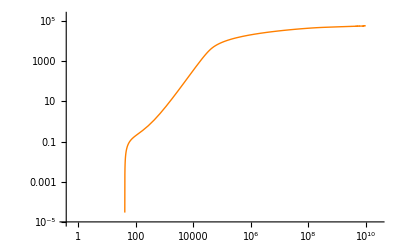

```mathematica
Show[pionpauli1]
```

```mathematica
protonpauli=LogLogPlot[ReplaceAll[ReplaceAll[(dedxpaulinondeg+dedxpaulideg) 5.*^5,{α->1/137,M->0.511,Z->1,n->8}],m->1000],{ϵ,1,10^10},PlotStyle->{Orange,Thick}];
```

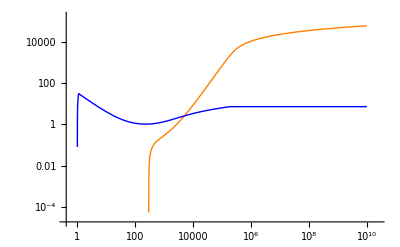

```mathematica
Show[protonpauli,proton]
```

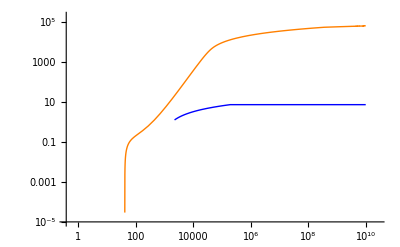

```mathematica
Show[pionpauli,pion]
```

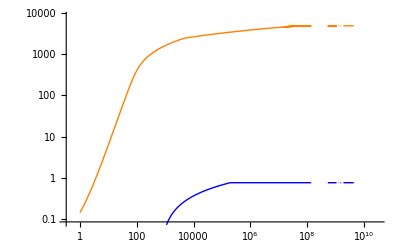

```mathematica
Show[electronpauli,electron]
```

#### Just examine the Coulomb Logarithm, find where scattering should “shut off” for protons and pions.

```mathematica
coulomblog={Max[Esc,0Elattice],Min[Ekin,Equant,M]}/.{Ef->(3 Pi^2 n)^(1/3)}/.{γ->1/Sqrt[1-β^2]}/.{β->(√ϵ √(2 m+ϵ))/(m+ϵ)}/.{α->1/137,M->12000,Z->6,n->0.8};
```

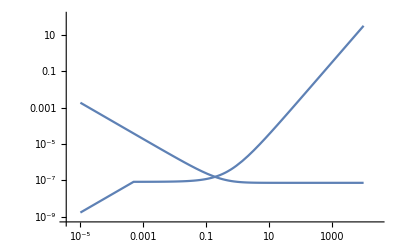

```mathematica
LogLogPlot[coulomblog/.m->0.511,{ϵ,0.00001,10^4}]
```

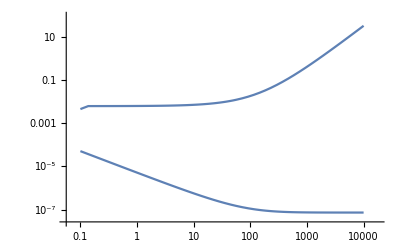

```mathematica
LogLogPlot[coulomblog/.m->140,{ϵ,0.1,10^4}]
```

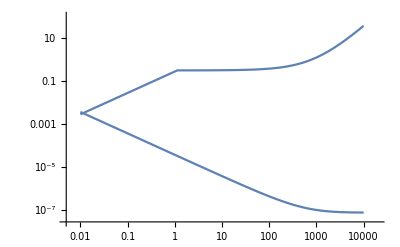

1/(9 M π ϵ (2 m+ϵ))Z^2 α^2 (m+ϵ)^2 (-(4 3^(2/3) n^(2/3) π^(1/3) Z^3 α^3 (m+ϵ)^2)/(M ϵ (2 m+ϵ))+Min[(2 M ϵ √(m^2/(m+ϵ)^2) (2 m+ϵ))/(2 m M+m^2 √(m^2/(m+ϵ)^2)+M^2 √(m^2/(m+ϵ)^2)),(2 Z^2 α^2 (m+ϵ)^2 Min[m,M]^2)/(m^2 M)]) (18 3^(2/3) n^(2/3) π^(4/3)-1/(M ϵ (2 m+ϵ))9 (12 n π Z^3 α^3 (m+ϵ)^2+3^(1/3) M n^(1/3) π^(2/3) ϵ (2 m+ϵ) Min[(2 M ϵ √(m^2/(m+ϵ)^2) (2 m+ϵ))/(2 m M+m^2 √(m^2/(m+ϵ)^2)+M^2 √(m^2/(m+ϵ)^2)),(2 Z^2 α^2 (m+ϵ)^2 Min[m,M]^2)/(m^2 M)])+2 ((48 3^(1/3) n^(4/3) π^(2/3) Z^6 α^6 (m+ϵ)^4)/(M^2 ϵ^2 (2 m+ϵ)^2)+1/(M ϵ (2 m+ϵ))4 3^(2/3) n^(2/3) π^(1/3) Z^3 α^3 (m+ϵ)^2 Min[(2 M ϵ √(m^2/(m+ϵ)^2) (2 m+ϵ))/(2 m M+m^2 √(m^2/(m+ϵ)^2)+M^2 √(m^2/(m+ϵ)^2)),(2 Z^2 α^2 (m+ϵ)^2 Min[m,M]^2)/(m^2 M)]+Min[(2 M ϵ √(m^2/(m+ϵ)^2) (2 m+ϵ))/(2 m M+m^2 √(m^2/(m+ϵ)^2)+M^2 √(m^2/(m+ϵ)^2)),(2 Z^2 α^2 (m+ϵ)^2 Min[m,M]^2)/(m^2 M)]^2))

ConditionalExpression[(2 5 (Log[Min[1/1,1]]-1))/(M ϵ (2 m+ϵ)),1]
 |  |  |  |

```mathematica
LogLogPlot[coulomblog/.m->1000,{ϵ,0.01,10^4}]
```